```mathematica
pathToProject="/media/my_extra_space/projects/1510GPCR/";
pathToDump=pathToProject<>"dumps/";
Get[pathToDump<>"fromSettingWeightsForConductingPCA.m"];
```

```mathematica
buf=structuresShort;
buf={{#[[1]][[1]]<>"_"<>#[[1]][[2]],#[[1]][[3]],numToFamily[#[[1]][[4]]],#[[1]][[5]],#[[1]][[6]]},#[[2]]}&/@buf;
numToFamily[number_]:=Module[{},If[number==0,Return["Unk"];,Return[families[[number]]];];];
structuresShort=buf;
```

```mathematica
calcDistance[set1Triplets_,set2Triplets_]:=Module[{differenceVector,squareDistance},differenceVector=set1Triplets-set2Triplets;
squareDistance=Plus@@(Norm[#]^2&/@differenceVector);
Return[Sqrt[squareDistance/Length[differenceVector]]];];
calcRmsd[set1Triplets_,set2Triplets_]:=Module[{covariance,v,s,w,rotMatrix,set1Reduced,set2Reduced},set1Reduced=(set1Tripletsᵀ-(Mean[#]&/@(set1Tripletsᵀ)))ᵀ;
set2Reduced=(set2Tripletsᵀ-(Mean[#]&/@(set2Tripletsᵀ)))ᵀ;
covariance=set1Reducedᵀ.set2Reduced;
{v,s,w}=SingularValueDecomposition[covariance];
rotMatrix=v.{{1.,0.,0.},{0.,1.,0.},{0.,0.,Sign[Det[w.vᵀ]]}}.wᵀ;
Return[calcDistance[set1Reduced.rotMatrix,set2Reduced]];];
alignYtoX[set1Triplets_,set2Triplets_]:=Module[{alignedSet,mean1Set,set1Reduced,set2Reduced,covariance,v,s,w,rotMatrix},mean1Set=(Mean[#]&/@(set1Tripletsᵀ));
set1Reduced=(set1Tripletsᵀ-mean1Set)ᵀ;
set2Reduced=(set2Tripletsᵀ-(Mean[#]&/@(set2Tripletsᵀ)))ᵀ;
covariance=set1Reducedᵀ.set2Reduced;
{v,s,w}=SingularValueDecomposition[covariance];
rotMatrix=v.{{1.,0.,0.},{0.,1.,0.},{0.,0.,Sign[Det[w.vᵀ]]}}.wᵀ;
alignedSet=set2Reduced.(rotMatrixᵀ);
alignedSet=(alignedSetᵀ+mean1Set)ᵀ;
Return[alignedSet];];

alignAllToMolecule[averageTriplet_]:=Module[{},
Do[
pdbCoordinates[[i]]=alignYtoX[averageTriplet,pdbCoordinates[[i]]];
,{i,1,numOfFiles}
];
];
```

```mathematica
means=Range[5];
means[[1]]=pdbCoordinates[[Position[structuresShortᵀ[[1]]ᵀ[[1]],"2RH1_A"][[1]][[1]]]];
Do[
alignAllToMolecule[means[[i-1]]];
means[[i]]=Mean[#]&/@(pdbCoordinatesᵀ);
,{i,2,5}
];

mean=means[[5]];
```

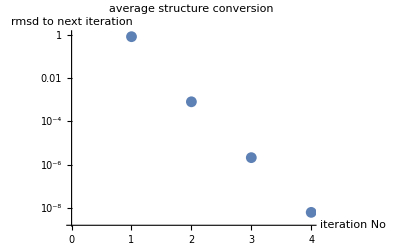

```mathematica
ListLogPlot[calcRmsd[means[[#]],means[[#+1]]]&/@Range[4], PlotLabel->"average structure conversion", AxesLabel->{"iteration No","rmsd to next iteration"}]
```

```mathematica
coordinates=Flatten[#]&/@pdbCoordinates;
zeroMean=Map[#-Flatten@mean&,coordinates];
covarianceMatrix=zeroMeanᵀ.zeroMean/numOfFiles;
eigenValues=Eigenvalues[covarianceMatrix];
eigenVectors=Eigenvectors[covarianceMatrix];
```

```mathematica
pcaProjections=(Total[eigenVectors[[#]]*zeroMeanᵀ])&/@Range[Length[eigenValues]];
pos1=Position[structuresShortᵀ[[1]]ᵀ[[1]],"1F88_A"][[1]][[1]];
pos2=Position[structuresShortᵀ[[1]]ᵀ[[1]],"3SN6_R"][[1]][[1]];
pos3=Position[structuresShortᵀ[[1]]ᵀ[[1]],"2RH1_A"][[1]][[1]];
pos4=Position[structuresShortᵀ[[1]]ᵀ[[1]],"4YAY_A"][[1]][[1]];
pos5=Position[structuresShortᵀ[[1]]ᵀ[[1]],"3OE8_A"][[1]][[1]];
pos6=Position[structuresShortᵀ[[1]]ᵀ[[1]],"3ZEV_A"][[1]][[1]];
If[pcaProjections[[1]][[pos2]]-pcaProjections[[1]][[pos1]]>0, ,pcaProjections[[1]]*=-1;eigenVectors[[1]]*=-1;];
If[pcaProjections[[2]][[pos1]]-pcaProjections[[2]][[pos3]]>0, ,pcaProjections[[2]]*=-1;eigenVectors[[2]]*=-1;];
If[pcaProjections[[3]][[pos4]]-pcaProjections[[3]][[pos3]]>0, ,pcaProjections[[3]]*=-1;eigenVectors[[3]]*=-1;];
If[pcaProjections[[4]][[pos6]]-pcaProjections[[4]][[pos5]]>0, ,pcaProjections[[4]]*=-1;eigenVectors[[4]]*=-1;];

evalMax=0.45;
evalsCumulative=evalMax (#/#[[-1]]&@Accumulate@eigenValues);
plotEigenValues=ListPlot[{eigenValues[[1;;25]]/((Length[coordinates[[1]]]/3)),evalsCumulative[[1;;25]]},Joined->True,PlotRange->{0,evalMax},PlotRangePadding->{0,0},ImageSize->1000,PlotMarkers->{Automatic,20},Frame->True,Epilog->(Text[Style[ToString@Round[(100/evalMax)*evalsCumulative[[#]]]<>"%",FontSize->13],{#+0.6,evalsCumulative[[#]]-0.003}]&/@Range[25]),FrameLabel->{{"Eigenvalue/\!\(\*SubscriptBox[\(N\), \(atoms\)]\) (\!\(\*SuperscriptBox[\(Å\), \(2\)]\))",""},{"Principal Component No.","Class A"}},LabelStyle->{16,GrayLevel[0]},PlotLegends->{"Eigenvalue/\!\(\*SubscriptBox[\(N\), \(atoms\)]\)","Cumulative"}];
Export[pathToProject<>"figures/cumulativeEigenvalues/"<>"cumulativeEigenValueAClassesUnweighted.png",plotEigenValues];
```

```mathematica
showFamilies[familyName_]:=Module[{shower},shower=(Select[structuresShort,#[[1]][[3]]==familyName&])ᵀ[[1]]ᵀ[[1]];
Return[Union[StringTake[#,4]&/@shower]];];

crossSize=0.005;
labelSize=0.015;

f1to2repulsive[r1_,r2_]:=If[r1==r2,0,Normalize[r2-r1] Min[10.,.0005/Norm[r2-r1]^12.]];
f1to2attractive[r1_,r2_]:=-10. Normalize[r2-r1] ((Norm[r2-r1]+Norm[r2-r1]^2)/labelSize);

(*
f1to2repulsive[r1_,r2_]:=If[r1==r2,0.,Normalize[r2-r1] Min[200.,0.000005/Norm[r2-r1]^6.]];
f1to2attractive[r1_,r2_]:=- Normalize[r2-r1] ((Norm[r2-r1]+Norm[r2-r1]^2)/labelSize);
*)
dt=0.001;
denominator=Sqrt[(Length[coordinates[[1]]]/3)];

plotPCiPCjwithHighlitedFams[pairs_,famsToHighlight_,showSubfamily_]:=Module[{plot,littles,coordStart,coordEnd,n,totalForces,listGathered,listGatheredAveraged,listGatheredAveragedTooltips,pos},
listGathered=Gather[{structuresShort,pcaProjections[[pairs[[1]]]],pcaProjections[[pairs[[2]]]]}ᵀ,StringTake[#1[[1]][[1]][[1]],4]==StringTake[#2[[1]][[1]][[1]],4]&];
listGatheredAveraged={Mean[#ᵀ[[2]]]/denominator,Mean[#ᵀ[[3]]]/denominator,{StringTake[#ᵀ[[1]][[1]][[1]][[1]],4],#ᵀ[[1]][[1]][[1]][[2]],#ᵀ[[1]][[1]][[1]][[3]]}}&/@listGathered;
listGatheredAveragedTooltips=Tooltip[{#[[1]],#[[2]]},#[[3]][[1]]<>" "<>#[[3]][[3]]<>"\n"<>(#[[3]][[2]])]&/@listGatheredAveraged;
littles=Select[listGatheredAveraged,Intersection[{#[[3]][[3]]},famsToHighlight]!={}&];
coordStart=littlesᵀ[[1;;2]]ᵀ;
coordEnd=coordStart;
n=Length@coordStart;
For[i=0,i<100,i++,totalForces=Plus@@#&/@Table[If[i==j,{0,0},f1to2repulsive[coordEnd[[j]],coordEnd[[i]]]],{i,1,n},{j,1,n}]+MapThread[f1to2attractive,{coordStart,coordEnd}];
coordEnd=coordEnd+dt totalForces;];

(littles[[#,1;;2]]=coordEnd[[#]])&/@Range[Length@coordEnd];

plot=ListPlot[listGatheredAveragedTooltips[[;;,{1,2}]],AspectRatio->1,PlotRange->All,ImageSize->(*1200*)4200,PlotMarkers->{Automatic,3},AxesLabel->("PC"<>(ToString@#<>", Å")&/@pairs),PlotLabel->("Class A unweighted, PC"<>ToString@pairs[[1]]<>" vs PC"<>ToString@pairs[[2]]),
PlotRangePadding->{.17,.3},PlotLegends->Row[{Style["RHO",Green],Style["ADRB2",Red],Style["ADRB1",Black],Style["ADORA2A",Blue],Style["Ntsr1",Magenta]},"\n"],
Epilog->Join[

MapThread[Line[{#1,#1+Normalize[#2-#1](Norm[#2-#1]-labelSize)}]&,{coordStart,coordEnd}],
{
Line[{
#[[1;;2]]-{crossSize,crossSize},
#[[1;;2]]+{crossSize,crossSize}
}],
Line[{
#[[1;;2]]-{-crossSize,crossSize},
#[[1;;2]]+{-crossSize,crossSize}
}]
}&/@coordStart,

{AbsolutePointSize[10],RGBColor[0,0,.8],AbsoluteThickness[3]}
,{AbsolutePointSize[5],Green},(pos=Position[listGatheredAveragedᵀ[[3]],#][[1,1]];
Point[listGatheredAveraged[[pos,{1,2}]]])&/@(Flatten@{showFamilies["RHO"],showFamilies["rho"]})
,{AbsolutePointSize[5],Red},(pos=Position[listGatheredAveragedᵀ[[3]],#][[1,1]];
Point[listGatheredAveraged[[pos,{1,2}]]])&/@showFamilies["ADRB2"]
,{AbsolutePointSize[5],Black},(pos=Position[listGatheredAveragedᵀ[[3]],#][[1,1]];
Point[listGatheredAveraged[[pos,{1,2}]]])&/@showFamilies["ADRB1"]
,{AbsolutePointSize[5],Blue},(pos=Position[listGatheredAveragedᵀ[[3]],#][[1,1]];
Point[listGatheredAveraged[[pos,{1,2}]]])&/@showFamilies["ADORA2A"]
,{AbsolutePointSize[5],Magenta},(pos=Position[listGatheredAveragedᵀ[[3]],#][[1,1]];
Point[listGatheredAveraged[[pos,{1,2}]]])&/@showFamilies["Ntsr1"]
,{AbsoluteThickness[1],Gray}
,Text[Style[
(
If[showSubfamily==True,
(ToString[#[[3]][[1]]]<>"\n"<>ToString[#[[3]][[3]]]),
ToString[#[[3]][[1]]]
]
),Blue,10, Bold],#[[1;;2]]]&/@littles,
Circle[#[[1;;2]],labelSize]&/@littles
]
];
Return[plot];
];
```

```mathematica
pc1pc2plot=plotPCiPCjwithHighlitedFams[{1,2},
{"CHRM2","Chrm3","ADRB1","ADRB2","DRD3","HRH1","HTR1B","HTR2B","CCR5","CXCR4","Ntsr1","OPRD1","OPRK1","Oprm1","OPRL1","F2R","RHO","rho","ADORA2A","P2RY12""Unk"},
True];
```

```mathematica
Export[pathToProject<>"figures/PCiPCj/"<>"pc1pc2Unweighted.png",pc1pc2plot];
```

```mathematica
eigenVectorsUnweighted=eigenVectors[[1;;numOfFiles]];
```

```mathematica
Save[pathToDump<>"eigenVectorsUnweighted.m",eigenVectorsUnweighted];
```